# Ground state Hamiltonian for polar molecules

## Gabriel Patenotte 4/16/23

# Setup

### Default options for plots, error messages, and colors

```mathematica
SetDirectory["/Users/gpatenotte/Documents/Research/Ni Group/Mathematica"];
SetOptions[Plot,BaseStyle->{FontFamily->"Arial",FontSize->20},TicksStyle->Directive[Black,10],Frame->True,FrameTicks->{Automatic,Automatic},ImagePadding->{{80,10},{80,10}},ImageSize->500,AxesLabel->{"",""},PlotStyle->Black]; 
SetOptions[ListPlot,BaseStyle->{FontFamily->"Arial",FontSize->20},TicksStyle->Directive[Black,10],Frame->True,FrameTicks->{Automatic,Automatic},ImagePadding->{{80,10},{80,10}},ImageSize->500,AxesLabel->{"",""}]; 
ParallelEvaluate[Off[ClebschGordan::tri]];
ParallelEvaluate[Off[ClebschGordan::phy]];
Off[ClebschGordan::tri];
Off[ClebschGordan::phy];
colors=RGBColor/@{"#408EC6","#7A2048","#1E2761","#89ABE3FF","#EA738DFF","#8BB9B9"};
```

### Supporting constants

#### Basis labels

```mathematica
bUC={"I1","mI1","I2","mI2","N","mN","S","mS"};
bI={"I1","I2","I","mI","N","mN","S","mS"};
bJ={"I1","mI1","I2","mI2","N","S","J","mJ"};
bIJ={"I1","I2","I","mI","N","S","J","mJ"};
bF={"I1","I2","I","N","S","J","F","mF"};
bF1={"I1","I2","mI2","N","F1","mF1","S","J"};
bF2={"I1","mI1","I2","N","F2","mF2","S","J"};
bN={"N","mN"};
b={bUC,bI,bJ,bIJ,bF,bF1,bF2,bN};
```

### Supporting functions

```mathematica
conj[x_]:=Module[{re,im},x/.(Complex[re_,im_]->Complex[re,-im])]; (*Replacement that gives the complex conjugate*)
J1dotJ2[J_,J1_,J2_]:=1/2(J(J+1)-J1(J1+1)-J2(J2+1))(*Dot product of two angular momenta*)
createSpace[aQN_Association]:=Module[{a},
a=Map[If[Length[#]==0,{#},#]&,aQN,1];
nℋ=Sum[(2I1+1)(2I2+1)(2N+1)(2S+1),{N,a["N"]},{S,a["S"]},{I1,a["I1"]},{I2,a["I2"]}]; (*number of states in Hilbert space*)
ℋ=IdentityMatrix[nℋ];
sℋ=Partition[ℋ,{nℋ,1}][[1]];
] (*example: aQN = Association["I1"->3/2, "I2"-> 7/2, "S"->0, "N"->{0,1}]*)
```

```mathematica
createLists[aQN_Association]:=Module[{a,spins},
a=Map[If[Length[#]==0,{#},#]&,aQN,1];
am={{I1,a["I1"]},{I2,a["I2"]},{S,a["S"]},{N,a["N"]}}; (*angular momentums*)
lUC=Flatten[Table[ToExpression[bUC],Evaluate[Sequence@@am],{mI1,-I1,I1},{mI2,-I2,I2},{mS,-S,S},{mN,-N,N}],7];
lI=Flatten[Table[ToExpression[bI],Evaluate[Sequence@@am],{I,Abs[I1-I2],I1+I2},{mI,-I,I},{mN,-N,N},{mS,-S,S}],7];
lJ=Flatten[Table[ToExpression[bJ],Evaluate[Sequence@@am],{mI1,-I1,I1},{mI2,-I2,I2},{J,Abs[N-S],N+S},{mJ,-J,J}],7];
lIJ=Flatten[Table[ToExpression[bIJ],Evaluate[Sequence@@am],{I,Abs[I1-I2],I1+I2},{mI,-I,I},{J,Abs[N-S],N+S},{mJ,-J,J}],7];
lF=Flatten[Table[ToExpression[bF],Evaluate[Sequence@@am],{I,Abs[I1-I2],I1+I2},{J,Abs[N-S],N+S},{F,Abs[I-J],I+J},{mF,-F,F}],7];
lF1=Flatten[Table[ToExpression[bF1],Evaluate[Sequence@@am],{mI2,-I2,I2},{J,Abs[N-S],N+S},{F1,Abs[I1-J],I1+J},{mF1,-F1,F1}],7];
lF2=Flatten[Table[ToExpression[bF2],Evaluate[Sequence@@am],{mI1,-I1,I1},{J,Abs[N-S],N+S},{F2,Abs[I2-J],I2+J},{mF2,-F2,F2}],7];
lN=Flatten[Table[ToExpression[bN],{N,a["N"]},{mN,-N,N}],1];
l = {lUC,lI,lJ,lIJ,lF,lF1,lF2,lN};
BtoL = AssociationThread[b->l];
LtoB = AssociationThread[l->b];
]
```

## Run

```mathematica
aQN = Association["I1"->3/2, "I2"-> 7/2, "S"->0, "N"->Range[0,10]];
createSpace[aQN] (*creates a Hilbert space*)
createLists[aQN] (*creates a list of the quantum numbers of each basis state*)
srE[{Nb_,Mb_},{Nk_,Mk_}]:=Abs[Nb-Nk]==1 ∧Abs[Mb-Mk]<=1
meE[{Nb_,Mb_},{Nk_,Mk_},q_:0]:=If[srE[{Nb,Mb},{Nk,Mk}],Sum[(-1)^mb √((2Nk+1)(2Nb+1))ThreeJSymbol[{Nb,-mb},{1,q},{Nk,mk}]ThreeJSymbol[{Nb,0},{1,0},{Nk,0}]conj[WignerD[{Nb,mb,Mb},θE,ϕE]]WignerD[{Nk,mk,Mk},θE,ϕE],{mb,-Nb,Nb},{mk,-Nk,Nk}],0]
```

```mathematica
HS=ParallelTable[meE[bra,ket],{bra,lN},{ket,lN}];
```

```mathematica
HSUC=With[{p=Position[bUC,#][[1,1]]&/@bN,pn=Position[bUC,#][[1,1]]&/@Complement[bUC,bN]},ParallelTable[With[{braP=Position[lN,lUC[[i,p]]][[1,1]],ketP=Position[lN,lUC[[j,p]]][[1,1]]},If[lUC[[i,pn]]==lUC[[j,pn]],HS[[braP,ketP]],0]],{i,1,nℋ},{j,1,nℋ}]];
```

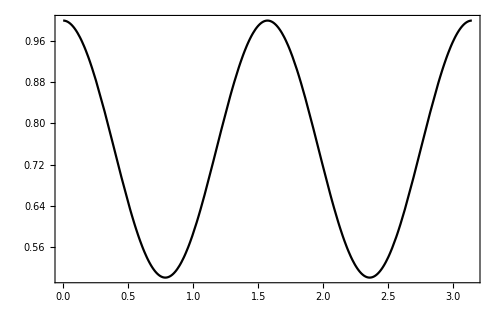

```mathematica
Plot[Abs[({{1, 0, 0}}).(Exp[-(ⅈ η)/2]({{Cos[θ]^2+Exp[ⅈ η] Sin[θ]^2, (1-Exp[ⅈ η])Cos[θ]Sin[θ], 0}, {(1-Exp[ⅈ η])Cos[θ]Sin[θ], Sin[θ]^2+Exp[ⅈ η] Cos[θ]^2, 0}, {0, 0, 1}}).({{1}, {0}, {0}}))/.η->π/2]^2,{θ,0,π}]
```

```mathematica
Export["HSUCbu.m",HSUC]
```

HSUCbu.m

```mathematica
HSUC//Length
```

3872